## Preliminaries

```mathematica
Clear["Global`*"]
SetDirectory[FileNameJoin[{NotebookDirectory[],"results/"}]]
```

/Users/marknovak/Git/aaaManuscripts/GeometricComplexity/mathematica/results

SC_2= -Log_ef(x|(Θ̂)_x)+k/2 Log_e(n/(2 π))+Log_e∫_Θ √(det I(Θ))ⅆΘ + o(1);
The first term is the likelihood. The second term is the parameter and sample size dependent component.
The third term containing I(Θ), the Expected Fisher Information Matrix, reflects the model's flexibility.
The Fisher information matrix is the Hessian of the negative log-likelihood or, equivalently, the negative Hessian of the log-likelihood.
The Observed Fisher information matrix is the Fisher information matrix evaluated at the MLE.
The Expected Fisher information matrix is the Fisher information matrix “of sample size 1” (Myung et al. 2006, below eqn. 10), i.e. the expectation of the Fisher matrix evaluated over the probability distribution of x_i samples (e.g., x_i \[Distributed] Poisson).  We also take the expectation over the (experiment’s) variables, which in the context of functional responses is Ν and P (and, in the general sense, time T, which we do not do here).
Structural complexity is the natural log of the integration (over all parameters) of the square root of the determinant of the Expected Fisher Information matrix (Myung et al. 2006, 3rd part of RHS of eqn. 10).
Structural complexity can only be compared between models having the same number of parameters (k).
In order to compare models having different numbers of parameters in terms of their “performance” requires also including the parameter-cost:    k/2Ln(n/(2 π))

### Define Functional Responses - Count of prey eaten

```mathematica
H1 = a Ν P T;
R = (a Ν P T)/P;
H2 = (a Ν P T)/(1+a h Ν);
HV = (a Ν P T)/P^m;
AG = (a Ν P T)/(P+a h Ν);
BD = (a Ν P T)/(1+a h Ν + γ (P-1));
CM = (a Ν P T)/((1+a h Ν)(1+γ (P-1)));
AA=(a Ν P T)/(P^m+a h Ν);
```

### Define Likelihood functions

Note: If x_i\[Distributed]Poission(λ_i) for i = 1,...,n are independent and λ = ∑ λ_i, then Y=∑λ_i\[Distributed]Poission(λ).     Therefore we can just replace ∑_(i=1)^n x_i→ x.  
(See https://en.wikipedia.org/wiki/Poisson_distribution#Properties)

See MLE.bias for derivation of logLikelihood
PoislL=-n λ-Log[∏_(i=1)^n x_i!]+Log[λ] ∑_(i=1)^n x_i
The second term (-Log[∏_(i=1)^n x_i!]) drops out in derivative anyway, so leave out.
Expectation will be for a sample size of 1, so substitute here to speed up.

```mathematica
PoislL[func_]:=-n func+Log[func] x/.{n->1}

lLH1Poiss[a_]:=PoislL[H1]
lLRPoiss[a_]:=PoislL[R]
lLHVPoiss[a_,m_]:=PoislL[HV]
lLAGPoiss[a_,h_]:=PoislL[AG]
lLH2Poiss[a_,h_]:=PoislL[H2]
lLBDPoiss[a_,h_,γ_]:=PoislL[BD]
lLCMPoiss[a_,h_,γ_]:=PoislL[CM]
lLAAPoiss[a_,h_,m_]:=PoislL[AA]
```

### Define functions to compute fisher matrix and expected fisher matrix

Definition using Hessian (applies under mild regularity conditions):

```mathematica
fisher[fun_,pars_]:=-D[Apply[fun,pars],{pars,2}]
```

Expected Fisher Matrix given experimental design

```mathematica
EFisher[FisherMatrix_,func_,PDistE_,ΝDistE_]:=
Expectation[
Expectation[FisherMatrix,x\[Distributed] PoissonDistribution[func]],
{P\[Distributed]PDistE, Ν\[Distributed]ΝDistE}]
```

### Define function for Determinant of Expected Fisher Matrix given experimental design and min and max limits on expected count of prey eaten

For the Poisson, the expected count of prey eaten equals λ.  We set the maximum count of consumed prey (in any treatment) to be equal to the number of prey in the maximum prey abundance treatment (λmax = Max[Νvals]) and the minimum to be zero prey eaten (λmin = 0).  The choice of λmax = Max[Νvals] is somewhat arbitrary, but seems logistically feasible and has some useful mathematical properties.  Truncation is necessary due to the non-identifiability of some parameter combinations for some models (e.g., any ‘a’ is possible given a higher enough ‘m’, and vice versa) and is applied to all models for comparability.

```mathematica
DetEFisherTrunc[FisherMatrix_,func_,PDistE_,ΝDistE_,λmin_,λmax_,subs_]:=
Det[
Expectation[
Expectation[Boole[λmin ≤ func≤λmax]FisherMatrix,x\[Distributed] PoissonDistribution[func]]//.subs,
{P\[Distributed]PDistE, Ν\[Distributed]ΝDistE}] 
]
```

### Define functions to create experimental designs (prey and predator abundance levels)

Linear series of prey abundance levels (starting at 3 for prey and 1 for predators)

```mathematica
PreyVals[n_]:=Table[i,{i,3,n+2}]
PredVals[n_]:=Table[i,{i,1,n}]

PreyVals[10]
PredVals[10]
```

{3,4,5,6,7,8,9,10,11,12}

{1,2,3,4,5,6,7,8,9,10}

Fibonacci series of prey abundance levels (starting at 3 for prey and 1 for predators)
(Note that Fibonacci[i] gives the ith Fibonacci number.)

```mathematica
PreyVals[n_]:=Table[Fibonacci[i],{i,4,n+3}] 
PredVals[n_]:=Table[Fibonacci[i],{i,2,n+1}]

PreyVals[10]
PredVals[10]
```

{3,5,8,13,21,34,55,89,144,233}

{1,2,3,5,8,13,21,34,55,89}

Functions to create equidistant points in log-space

```mathematica
logSpace[a_?Positive,b_?Positive,n_]:=Exp@Range[Log@a,Log@b,Log[b/a]/(n-1)]
log2Space[a_,b_,n_]:=2^Range[a,b,(b-a)/(n-1)]
logGRSpace[a_,b_,n_]:=Round[GoldenRatio^Range[a,b,(b-a)/(n-1)]]
```

```mathematica
log2Space[1,10,10]
logGRSpace[0,10,10]
```

{2,4,8,16,32,64,128,256,512,1024}

{1,2,3,5,8,14,25,42,72,123}

GoldenRatio series of prey abundance levels (starting at 3 for prey and 1 for predators)
enabling the generation of arbitrary numbers of equidistant points between min and (specified) max abundances.
The series will be approximately Fibonacci when PreyMax is set to Fibonacci[n] for a desired series length n.

```mathematica
PreyVals[n_,PreyMax_]:=logGRSpace[2,Log[GoldenRatio,PreyMax]+3,n];
PredVals[n_,PredMax_]:=logGRSpace[0,Log[GoldenRatio,PredMax]+1,n];

PreyVals[10,Fibonacci[10]]
PredVals[10,Fibonacci[10]]

PredVals[8,Fibonacci[10]]
PredVals[6,Fibonacci[10]]
PredVals[3,Fibonacci[10]]
```

{3,4,7,12,19,32,52,86,141,233}

{1,2,3,4,7,12,20,33,54,89}

{1,2,4,7,13,25,47,89}

{1,2,6,15,36,89}

{1,9,89}

Example use for generating series of increasing length and increasing maximum value:

```mathematica
ParallelTable[
{PreyVals[i,Fibonacci[i]],PredVals[j,Fibonacci[j]]},
{i, 5,13},{j,2,8}
];
%//TableForm
```

3 | 4 | 7 | 13 | 21
1 | 2 |  |  |  | 3 | 4 | 7 | 13 | 21
1 | 2 | 3 |  |  | 3 | 4 | 7 | 13 | 21
1 | 2 | 3 | 5 |  | 3 | 4 | 7 | 13 | 21
1 | 2 | 3 | 5 | 8 | 3 | 4 | 7 | 13 | 21 | 
1 | 2 | 3 | 5 | 8 | 13 | 3 | 4 | 7 | 13 | 21 |  | 
1 | 2 | 3 | 5 | 8 | 13 | 21 | 3 | 4 | 7 | 13 | 21 |  |  | 
1 | 2 | 3 | 5 | 7 | 12 | 21 | 34
3 | 4 | 7 | 12 | 20 | 34
1 | 2 |  |  |  |  | 3 | 4 | 7 | 12 | 20 | 34
1 | 2 | 3 |  |  |  | 3 | 4 | 7 | 12 | 20 | 34
1 | 2 | 3 | 5 |  |  | 3 | 4 | 7 | 12 | 20 | 34
1 | 2 | 3 | 5 | 8 |  | 3 | 4 | 7 | 12 | 20 | 34
1 | 2 | 3 | 5 | 8 | 13 | 3 | 4 | 7 | 12 | 20 | 34 | 
1 | 2 | 3 | 5 | 8 | 13 | 21 | 3 | 4 | 7 | 12 | 20 | 34 |  | 
1 | 2 | 3 | 5 | 7 | 12 | 21 | 34
3 | 4 | 7 | 12 | 20 | 33 | 55
1 | 2 |  |  |  |  |  | 3 | 4 | 7 | 12 | 20 | 33 | 55
1 | 2 | 3 |  |  |  |  | 3 | 4 | 7 | 12 | 20 | 33 | 55
1 | 2 | 3 | 5 |  |  |  | 3 | 4 | 7 | 12 | 20 | 33 | 55
1 | 2 | 3 | 5 | 8 |  |  | 3 | 4 | 7 | 12 | 20 | 33 | 55
1 | 2 | 3 | 5 | 8 | 13 |  | 3 | 4 | 7 | 12 | 20 | 33 | 55
1 | 2 | 3 | 5 | 8 | 13 | 21 | 3 | 4 | 7 | 12 | 20 | 33 | 55 | 
1 | 2 | 3 | 5 | 7 | 12 | 21 | 34
3 | 4 | 7 | 12 | 20 | 32 | 54 | 89
1 | 2 |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 20 | 32 | 54 | 89
1 | 2 | 3 |  |  |  |  |  | 3 | 4 | 7 | 12 | 20 | 32 | 54 | 89
1 | 2 | 3 | 5 |  |  |  |  | 3 | 4 | 7 | 12 | 20 | 32 | 54 | 89
1 | 2 | 3 | 5 | 8 |  |  |  | 3 | 4 | 7 | 12 | 20 | 32 | 54 | 89
1 | 2 | 3 | 5 | 8 | 13 |  |  | 3 | 4 | 7 | 12 | 20 | 32 | 54 | 89
1 | 2 | 3 | 5 | 8 | 13 | 21 |  | 3 | 4 | 7 | 12 | 20 | 32 | 54 | 89
1 | 2 | 3 | 5 | 7 | 12 | 21 | 34
3 | 4 | 7 | 12 | 19 | 32 | 53 | 87 | 144
1 | 2 |  |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 32 | 53 | 87 | 144
1 | 2 | 3 |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 32 | 53 | 87 | 144
1 | 2 | 3 | 5 |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 32 | 53 | 87 | 144
1 | 2 | 3 | 5 | 8 |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 32 | 53 | 87 | 144
1 | 2 | 3 | 5 | 8 | 13 |  |  |  | 3 | 4 | 7 | 12 | 19 | 32 | 53 | 87 | 144
1 | 2 | 3 | 5 | 8 | 13 | 21 |  |  | 3 | 4 | 7 | 12 | 19 | 32 | 53 | 87 | 144
1 | 2 | 3 | 5 | 7 | 12 | 21 | 34 | 
3 | 4 | 7 | 12 | 19 | 32 | 52 | 86 | 141 | 233
1 | 2 |  |  |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 32 | 52 | 86 | 141 | 233
1 | 2 | 3 |  |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 32 | 52 | 86 | 141 | 233
1 | 2 | 3 | 5 |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 32 | 52 | 86 | 141 | 233
1 | 2 | 3 | 5 | 8 |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 32 | 52 | 86 | 141 | 233
1 | 2 | 3 | 5 | 8 | 13 |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 32 | 52 | 86 | 141 | 233
1 | 2 | 3 | 5 | 8 | 13 | 21 |  |  |  | 3 | 4 | 7 | 12 | 19 | 32 | 52 | 86 | 141 | 233
1 | 2 | 3 | 5 | 7 | 12 | 21 | 34 |  | 
3 | 4 | 7 | 12 | 19 | 31 | 52 | 85 | 140 | 229 | 377
1 | 2 |  |  |  |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 31 | 52 | 85 | 140 | 229 | 377
1 | 2 | 3 |  |  |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 31 | 52 | 85 | 140 | 229 | 377
1 | 2 | 3 | 5 |  |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 31 | 52 | 85 | 140 | 229 | 377
1 | 2 | 3 | 5 | 8 |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 31 | 52 | 85 | 140 | 229 | 377
1 | 2 | 3 | 5 | 8 | 13 |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 31 | 52 | 85 | 140 | 229 | 377
1 | 2 | 3 | 5 | 8 | 13 | 21 |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 31 | 52 | 85 | 140 | 229 | 377
1 | 2 | 3 | 5 | 7 | 12 | 21 | 34 |  |  | 
3 | 4 | 7 | 12 | 19 | 31 | 51 | 84 | 138 | 226 | 372 | 610
1 | 2 |  |  |  |  |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 31 | 51 | 84 | 138 | 226 | 372 | 610
1 | 2 | 3 |  |  |  |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 31 | 51 | 84 | 138 | 226 | 372 | 610
1 | 2 | 3 | 5 |  |  |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 31 | 51 | 84 | 138 | 226 | 372 | 610
1 | 2 | 3 | 5 | 8 |  |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 31 | 51 | 84 | 138 | 226 | 372 | 610
1 | 2 | 3 | 5 | 8 | 13 |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 31 | 51 | 84 | 138 | 226 | 372 | 610
1 | 2 | 3 | 5 | 8 | 13 | 21 |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 31 | 51 | 84 | 138 | 226 | 372 | 610
1 | 2 | 3 | 5 | 7 | 12 | 21 | 34 |  |  |  | 
3 | 4 | 7 | 12 | 19 | 31 | 51 | 83 | 137 | 224 | 367 | 602 | 987
1 | 2 |  |  |  |  |  |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 31 | 51 | 83 | 137 | 224 | 367 | 602 | 987
1 | 2 | 3 |  |  |  |  |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 31 | 51 | 83 | 137 | 224 | 367 | 602 | 987
1 | 2 | 3 | 5 |  |  |  |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 31 | 51 | 83 | 137 | 224 | 367 | 602 | 987
1 | 2 | 3 | 5 | 8 |  |  |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 31 | 51 | 83 | 137 | 224 | 367 | 602 | 987
1 | 2 | 3 | 5 | 8 | 13 |  |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 31 | 51 | 83 | 137 | 224 | 367 | 602 | 987
1 | 2 | 3 | 5 | 8 | 13 | 21 |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 31 | 51 | 83 | 137 | 224 | 367 | 602 | 987
1 | 2 | 3 | 5 | 7 | 12 | 21 | 34 |  |  |  |  |

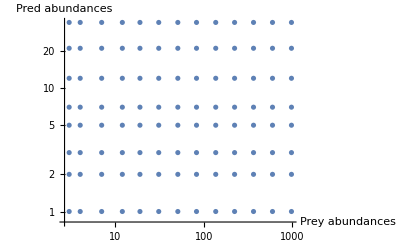

```mathematica
ListPlot[Tuples[{PreyVals[13,Fibonacci[13]],PredVals[8,Fibonacci[8]]}],
ScalingFunctions->{"Log","Log"},
AxesLabel->{"Prey abundances","Pred abundances"}]
```

Example use for generating series of varying length and constant maximum value:

```mathematica
ParallelTable[
{PreyVals[i,Fibonacci[13]],PredVals[j,Fibonacci[5]]},
{i, 5,13},{j,2,5}
];
%//TableForm
```

3 | 12 | 51 | 224 | 987
1 | 8 |  |  |  | 3 | 12 | 51 | 224 | 987
1 | 3 | 8 |  |  | 3 | 12 | 51 | 224 | 987
1 | 2 | 4 | 8 |  | 3 | 12 | 51 | 224 | 987
1 | 2 | 3 | 5 | 8
3 | 9 | 28 | 92 | 301 | 987
1 | 8 |  |  |  |  | 3 | 9 | 28 | 92 | 301 | 987
1 | 3 | 8 |  |  |  | 3 | 9 | 28 | 92 | 301 | 987
1 | 2 | 4 | 8 |  |  | 3 | 9 | 28 | 92 | 301 | 987
1 | 2 | 3 | 5 | 8 | 
3 | 7 | 19 | 51 | 137 | 367 | 987
1 | 8 |  |  |  |  |  | 3 | 7 | 19 | 51 | 137 | 367 | 987
1 | 3 | 8 |  |  |  |  | 3 | 7 | 19 | 51 | 137 | 367 | 987
1 | 2 | 4 | 8 |  |  |  | 3 | 7 | 19 | 51 | 137 | 367 | 987
1 | 2 | 3 | 5 | 8 |  | 
3 | 6 | 14 | 33 | 78 | 181 | 423 | 987
1 | 8 |  |  |  |  |  |  | 3 | 6 | 14 | 33 | 78 | 181 | 423 | 987
1 | 3 | 8 |  |  |  |  |  | 3 | 6 | 14 | 33 | 78 | 181 | 423 | 987
1 | 2 | 4 | 8 |  |  |  |  | 3 | 6 | 14 | 33 | 78 | 181 | 423 | 987
1 | 2 | 3 | 5 | 8 |  |  | 
3 | 5 | 12 | 24 | 51 | 107 | 224 | 470 | 987
1 | 8 |  |  |  |  |  |  |  | 3 | 5 | 12 | 24 | 51 | 107 | 224 | 470 | 987
1 | 3 | 8 |  |  |  |  |  |  | 3 | 5 | 12 | 24 | 51 | 107 | 224 | 470 | 987
1 | 2 | 4 | 8 |  |  |  |  |  | 3 | 5 | 12 | 24 | 51 | 107 | 224 | 470 | 987
1 | 2 | 3 | 5 | 8 |  |  |  | 
3 | 5 | 10 | 19 | 37 | 71 | 137 | 264 | 511 | 987
1 | 8 |  |  |  |  |  |  |  |  | 3 | 5 | 10 | 19 | 37 | 71 | 137 | 264 | 511 | 987
1 | 3 | 8 |  |  |  |  |  |  |  | 3 | 5 | 10 | 19 | 37 | 71 | 137 | 264 | 511 | 987
1 | 2 | 4 | 8 |  |  |  |  |  |  | 3 | 5 | 10 | 19 | 37 | 71 | 137 | 264 | 511 | 987
1 | 2 | 3 | 5 | 8 |  |  |  |  | 
3 | 5 | 9 | 16 | 28 | 51 | 92 | 167 | 301 | 545 | 987
1 | 8 |  |  |  |  |  |  |  |  |  | 3 | 5 | 9 | 16 | 28 | 51 | 92 | 167 | 301 | 545 | 987
1 | 3 | 8 |  |  |  |  |  |  |  |  | 3 | 5 | 9 | 16 | 28 | 51 | 92 | 167 | 301 | 545 | 987
1 | 2 | 4 | 8 |  |  |  |  |  |  |  | 3 | 5 | 9 | 16 | 28 | 51 | 92 | 167 | 301 | 545 | 987
1 | 2 | 3 | 5 | 8 |  |  |  |  |  | 
3 | 4 | 8 | 13 | 23 | 39 | 67 | 114 | 196 | 336 | 576 | 987
1 | 8 |  |  |  |  |  |  |  |  |  |  | 3 | 4 | 8 | 13 | 23 | 39 | 67 | 114 | 196 | 336 | 576 | 987
1 | 3 | 8 |  |  |  |  |  |  |  |  |  | 3 | 4 | 8 | 13 | 23 | 39 | 67 | 114 | 196 | 336 | 576 | 987
1 | 2 | 4 | 8 |  |  |  |  |  |  |  |  | 3 | 4 | 8 | 13 | 23 | 39 | 67 | 114 | 196 | 336 | 576 | 987
1 | 2 | 3 | 5 | 8 |  |  |  |  |  |  | 
3 | 4 | 7 | 12 | 19 | 31 | 51 | 83 | 137 | 224 | 367 | 602 | 987
1 | 8 |  |  |  |  |  |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 31 | 51 | 83 | 137 | 224 | 367 | 602 | 987
1 | 3 | 8 |  |  |  |  |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 31 | 51 | 83 | 137 | 224 | 367 | 602 | 987
1 | 2 | 4 | 8 |  |  |  |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 31 | 51 | 83 | 137 | 224 | 367 | 602 | 987
1 | 2 | 3 | 5 | 8 |  |  |  |  |  |  |  |

### Define master Geometric Complexity function w/ options

```mathematica
Clear[GeomComplexTrunc]
GeomComplexTrunc[
Νvalues_,
Pvalues_,
ModelSetParNum_:1,
Tval_:1,
aMax_: 1000, 
NIntMethod_:"LocalAdaptive",
accgoal_:3,
maxRec_:500,
e_:10]:=
Module[
{Νvals=Νvalues,Pvals=Pvalues},
Νprobs=ConstantArray[1/Length[Νvals],Length[Νvals]];Pprobs=ConstantArray[1/Length[Pvals],Length[Pvals]];
ΝDistE=EmpiricalDistribution[Νprobs->Νvals];
PDistE=EmpiricalDistribution[Pprobs->Pvals];
subs={T-> Tval};

PΝrats=Sort[DeleteDuplicates[Join@@Outer[Divide,Pvals,Νvals]]];
ParmRangeA={
{a,0,aMax},
DeleteDuplicates[Flatten[{{h},Sort[{0,PΝrats,1,10^e},Less]}]],
DeleteDuplicates[Flatten[{{γ},Sort[{0,1/Pvals,1,10^e},Less]}]],
DeleteDuplicates[Flatten[{{m},Sort[{0,PΝrats,1,10},Less]}]]
};

Which[ModelSetParNum==1,

FisherH1Poiss=fisher[lLH1Poiss,{a}];
DetH1Trunc=DetEFisherTrunc[FisherH1Poiss,H1,PDistE,ΝDistE,0,Max[Νvals],subs];

FisherRPoiss=fisher[lLRPoiss,{a}];
DetRTrunc=DetEFisherTrunc[FisherRPoiss,R,PDistE,ΝDistE,0,Max[Νvals],subs];

NIntH1Trunc=Log[NIntegrate[Sqrt[DetH1Trunc],
ParmRangeA[[1]],
AccuracyGoal->accgoal,
Method->NIntMethod,
MaxRecursion->maxRec]];

NIntRTrunc=Log[NIntegrate[Sqrt[DetRTrunc],
ParmRangeA[[1]],
AccuracyGoal->accgoal,
Method->NIntMethod,
MaxRecursion->maxRec]];

{NIntH1Trunc,NIntRTrunc, 
NIntRTrunc/NIntH1Trunc}

, (* End of ModelSetParNum=1*)

ModelSetParNum==2,

FisherHVPoiss=fisher[lLHVPoiss,{a,m}];DetHVTrunc=DetEFisherTrunc[FisherHVPoiss,HV,PDistE,ΝDistE,0,Max[Νvals],subs];

FisherH2Poiss=fisher[lLH2Poiss,{a, h}];
DetH2Trunc=DetEFisherTrunc[FisherH2Poiss,H2,PDistE,ΝDistE,0,Max[Νvals],subs];

FisherAGPoiss=fisher[lLAGPoiss,{a, h}];
DetAGTrunc=DetEFisherTrunc[FisherAGPoiss,AG,PDistE,ΝDistE,0,Max[Νvals],subs];


NIntHVTrunc=Log[NIntegrate[Sqrt[DetHVTrunc],
ParmRangeA[[1]],
ParmRangeA[[4]],
AccuracyGoal->accgoal,
Method->NIntMethod,
MaxRecursion->maxRec]];

NIntH2Trunc=Log[NIntegrate[Sqrt[DetH2Trunc],
ParmRangeA[[1]],
ParmRangeA[[2]],
AccuracyGoal->accgoal,
Method->NIntMethod,
MaxRecursion->maxRec]];

NIntAGTrunc=Log[NIntegrate[Sqrt[DetAGTrunc],
ParmRangeA[[1]],
ParmRangeA[[2]],
AccuracyGoal->accgoal,
Method->NIntMethod,
MaxRecursion->maxRec]];

{NIntHVTrunc, NIntH2Trunc, NIntAGTrunc, 
NIntHVTrunc/NIntH2Trunc,NIntAGTrunc/NIntH2Trunc}

, (* End of ModelSetParNum=2*)

ModelSetParNum==3,

FisherBDPoiss=fisher[lLBDPoiss,{a, h,γ}];
DetBDTrunc=DetEFisherTrunc[FisherBDPoiss,BD,PDistE,ΝDistE,0,Max[Νvals],subs];

FisherCMPoiss=fisher[lLCMPoiss,{a, h,γ}];
DetCMTrunc=DetEFisherTrunc[FisherCMPoiss,CM,PDistE,ΝDistE,0,Max[Νvals],subs];

FisherAAPoiss=fisher[lLAAPoiss,{a, h,m}];
DetAATrunc=DetEFisherTrunc[FisherAAPoiss,AA,PDistE,ΝDistE,0,Max[Νvals],subs];

NIntBDTrunc=Log[NIntegrate[Sqrt[DetBDTrunc],
ParmRangeA[[1]],
ParmRangeA[[2]],
ParmRangeA[[3]],
AccuracyGoal->accgoal,
Method-> NIntMethod]];

NIntCMTrunc=Log[NIntegrate[Sqrt[DetCMTrunc],
ParmRangeA[[1]],
ParmRangeA[[2]],
ParmRangeA[[3]],
AccuracyGoal->accgoal,
Method->NIntMethod,
MaxRecursion->maxRec]];

NIntAATrunc=Log[NIntegrate[Sqrt[DetAATrunc],
ParmRangeA[[1]],
ParmRangeA[[2]],
ParmRangeA[[4]],
AccuracyGoal->accgoal,
Method->NIntMethod,
MaxRecursion->maxRec]];

{NIntBDTrunc,NIntCMTrunc,NIntAATrunc,
NIntCMTrunc/NIntBDTrunc,NIntAATrunc/NIntBDTrunc}

] (* End of ModelSetParNum=3*)
]
```

## Apply across designs

```mathematica
PreyMinLevels=5;
PreyMaxLevels=9; (*13*)
PredMinLevels=2;
PredMaxLevels=5; (*8*)
```

```mathematica
GeomCompP1var=
Flatten[
ParallelTable[
Flatten[{
Max[PreyVals[i,Fibonacci[i]]],
Max[PredVals[j,Fibonacci[j]]],
GeomComplexTrunc[PreyVals[i,Fibonacci[i]],PredVals[j,Fibonacci[j]],ModelSetParNum= 1]}],
{i, PreyMinLevels,PreyMaxLevels},{j,PredMinLevels,PredMaxLevels}
],
1];
Save["GeomCompP1var.txt",GeomCompP1var]
```

```mathematica
GeomCompP1fix=
Flatten[
ParallelTable[
Flatten[{
Length[PreyVals[i,Fibonacci[PreyMaxLevels]]],
Length[PredVals[j,Fibonacci[PredMaxLevels]]],
GeomComplexTrunc[PreyVals[i,Fibonacci[PreyMaxLevels]],PredVals[j,Fibonacci[PredMaxLevels]],ModelSetParNum= 1]}],
{i, PreyMinLevels,PreyMaxLevels},{j,PredMinLevels,PredMaxLevels}
],
1];
Save["GeomCompP1fix.txt",GeomCompP1fix]
```

```mathematica
GeomCompP2var=
Flatten[
ParallelTable[
Flatten[{
Max[PreyVals[i,Fibonacci[i]]],
Max[PredVals[j,Fibonacci[j]]],
GeomComplexTrunc[PreyVals[i,Fibonacci[i]],PredVals[j,Fibonacci[j]],ModelSetParNum= 2]}],
{i, PreyMinLevels,PreyMaxLevels},{j,PredMinLevels,PredMaxLevels}
],
1];
Save["GeomCompP2var.txt",GeomCompP2var]
```

$Aborted

```mathematica
GeomCompP2fix=
Flatten[
ParallelTable[
Flatten[{
Length[PreyVals[i,Fibonacci[PreyMaxLevels]]],
Length[PredVals[j,Fibonacci[PredMaxLevels]]],
GeomComplexTrunc[PreyVals[i,Fibonacci[PreyMaxLevels]],PredVals[j,Fibonacci[PredMaxLevels]],ModelSetParNum= 2]}],
{i, PreyMinLevels,PreyMaxLevels},{j,PredMinLevels,PredMaxLevels}
],
1];
Save["GeomCompP2fix.txt",GeomCompP2fix]
```

```mathematica
GeomCompP3var=
Flatten[
ParallelTable[
Flatten[{
Max[PreyVals[i,Fibonacci[i]]],
Max[PredVals[j,Fibonacci[j]]],
GeomComplexTrunc[PreyVals[i,Fibonacci[i]],PredVals[j,Fibonacci[j]],ModelSetParNum= 3]}],
{i, PreyMinLevels,PreyMaxLevels},{j,PredMinLevels,PredMaxLevels}
],
1];
Save["GeomCompP3var.txt",GeomCompP3var]
```

```mathematica
GeomCompP3fix=
Flatten[
ParallelTable[
Flatten[{
Length[PreyVals[i,Fibonacci[PreyMaxLevels]]],
Length[PredVals[j,Fibonacci[PredMaxLevels]]],
GeomComplexTrunc[PreyVals[i,Fibonacci[PreyMaxLevels]],PredVals[j,Fibonacci[PredMaxLevels]],ModelSetParNum= 3]}],
{i, PreyMinLevels,PreyMaxLevels},{j,PredMinLevels,PredMaxLevels}
],
1];
Save["GeomCompP3fix.txt",GeomCompP3fix]
```